## Module for cubic splines

See: Algorithm for computing natural cubic splines
and: Module for cubic splines

-Graphics-

```mathematica
vv={{0.005,4.892186615295462},{0.015,14.676559845886388},{0.025,24.46093307647731},{0.035,34.24530630706823},{0.045,44.02967953765916},{0.055,53.814052768250086},{0.065,63.59842599884101},{0.075,73.38279922943194},{0.085,83.16717246002285},{0.095,92.95154569061378},{0.105,102.7359189212047},{0.115,86.31950198802133},{0.125,69.6878656320079},{0.135,54.19364223592307},{0.145,40.74442799816186},{0.155,29.856496631443783},{0.165,21.704478647360023},{0.175,16.131181083102938},{0.185,12.681626472973567},{0.195,10.719645882407347},{0.205,9.605206765579736},{0.215,8.848641162475756},{0.225,8.172566961796365},{0.235,7.479768896205763},{0.245,6.776486573968014},{0.255,6.102292085631324},{0.265,5.490315366328966},{0.275,4.955681154780191},{0.285,4.498774592953758},{0.295,4.11156325108247},{0.305,3.78254002926276},{0.315,3.502154452713242},{0.325,3.272187071110192},{0.335,3.1194611713496467},{0.345,3.10924073238575},{0.355,3.3497547076034233},{0.365,3.9785585926517593},{0.375,5.125155769282402},{0.385,6.854046870524738},{0.395,9.108141754137977},{0.405,11.685798013845789},{0.415,14.277493291642157},{0.425,16.553052061729908},{0.435,18.254373471058592},{0.445,19.248734404652193},{0.455,19.530806495811483},{0.465,19.190989910182505},{0.475,18.37349989105915},{0.485,17.2389346784465},{0.495,15.936928632905715}};
```

## Computation of Natural Cubic Splines

Input: a set of k + 1 coordinates
Output: a spline as a set of polynomial pieces, each represented by a 5-tuple.

-Graphics-

```mathematica
vv⟦{1,5,11,15,20}⟧//N
{x,y}=Transpose@%;
k=Length@x-1
```

{{0.005,4.89219},{0.045,44.0297},{0.105,102.736},{0.145,40.7444},{0.195,10.7196}}

4

```mathematica
a=y;
h=Table[x⟦i+1⟧-x⟦i⟧,{i,1,k}];
alp=Join[{0},Table[3(a⟦i+1⟧-a⟦i⟧)/h⟦i⟧-3(a⟦i⟧-a⟦i-1⟧)/h⟦i-1⟧,
{i,2,k}]];
```

```mathematica
b=d=mu=Table[0,{k}];
c=l=z=Table[0,{k+1}];
l⟦1⟧=1;mu⟦1⟧=z⟦1⟧=0;
```

```mathematica
Do[
l⟦i⟧=2(x⟦i+1⟧-x⟦i-1⟧)-h⟦i-1⟧mu⟦i-1⟧;
mu⟦i⟧=h⟦i⟧/l⟦i⟧;
z⟦i⟧=(alp⟦i⟧-h⟦i-1⟧z⟦i-1⟧)/l⟦i⟧,
{i,2,k}
]
```

```mathematica
l⟦k+1⟧=1;z⟦k+1⟧=c⟦k+1⟧=0;
```

```mathematica
Do[
c⟦j⟧=z⟦j⟧-mu⟦j⟧c⟦j+1⟧;
b⟦j⟧=(a⟦j+1⟧-a⟦j⟧)/h⟦j⟧-h⟦j⟧(c⟦j+1⟧+2c⟦j⟧)/3;
d⟦j⟧=(c⟦j+1⟧-c⟦j⟧)/(3h⟦j⟧),
{j,k,1,-1}
]
```

```mathematica
vvSpline[v_]=Piecewise[Table[
{a⟦i⟧+b⟦i⟧(v-x⟦i⟧)+c⟦i⟧(v-x⟦i⟧)^2+d⟦i⟧(v-x⟦i⟧)^3,v≤x⟦i+1⟧},
{i,1,k}
],Indeterminate]
```

Piecewise[{{4.89219+788.558 (-0.005+v)+118674. (-0.005+v)^3, v≤0.045}, {44.0297+1358.2 (-0.045+v)+14240.9 (-0.045+v)^2-342837. (-0.045+v)^3, v≤0.105}, {102.736-635.533 (-0.105+v)-47469.7 (-0.105+v)^2+615334. (-0.105+v)^3, v≤0.145}, {40.7444-1479.51 (-0.145+v)+26370.4 (-0.145+v)^2-175802. (-0.145+v)^3, v≤0.195}, {Indeterminate, True}}]

```mathematica
Table[{v,vvSpline[v]},{v,0,0.2,0.01}]//TableForm
```

0. | 0.93456
0.01 | 8.84981
0.02 | 17.1211
0.03 | 26.4604
0.04 | 37.5799
0.05 | 51.1338
0.06 | 66.4497
0.07 | 81.5283
0.08 | 94.3125
0.09 | 102.745
0.1 | 104.77
0.11 | 98.4484
0.12 | 84.599
0.13 | 66.7936
0.14 | 48.7243
0.15 | 33.9842
0.16 | 23.8918
0.17 | 17.4913
0.18 | 13.7278
0.19 | 11.5466
0.2 | Indeterminate

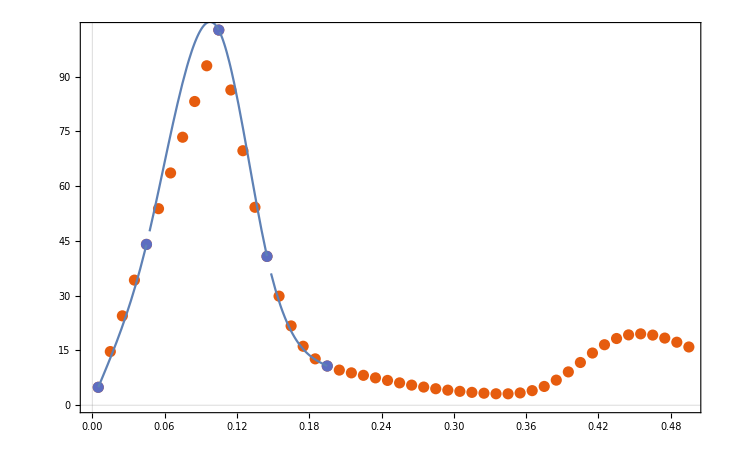

```mathematica
Show[
ListPlot[{vv,Transpose@{x,y}},PlotTheme->"Scientific"],
Plot[vvSpline[v],{v,x⟦1⟧,x⟦k+1⟧}]
]
```